```mathematica
Max[RandomVariate[UniformDistribution[{0,1}],{100,3}]]
```

0.99461

```mathematica
r:= RandomVariate[UniformDistribution[]];
ta = Table[a=r;
b = r;
c = r;
{z = Max[a,b,c],y=Min[a,b,c],z-y},{10^6}];
W=Transpose[ta][[3]];
```

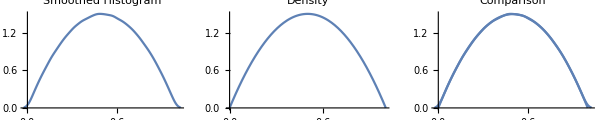

```mathematica
GraphicsRow[{pl1=SmoothHistogram[W,PlotStyle->"Red",PlotLabel->"Smoothed Histogram"],pl2=Plot[6{w-w^2},{w,0,1},PlotLabel->Density],Show[pl1,pl2,PlotLabel-> Comparison]}]
```

```mathematica
□/□
```